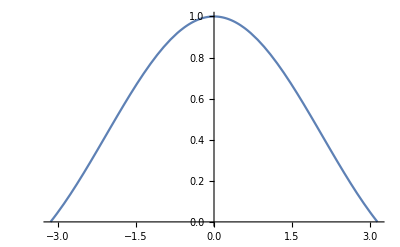

```mathematica
Plot[Sinc[x],{x,-π,π},PlotRange->Full]
```

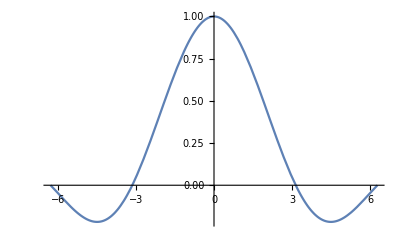

```mathematica
Plot[Sinc[x],{x,-2π,2π},PlotRange->Full]
```

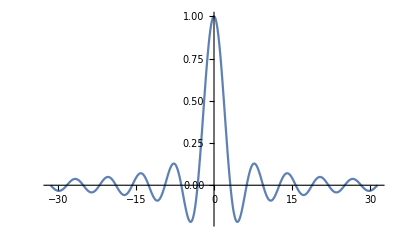

```mathematica
Plot[Sinc[x],{x,-10π,10π},PlotRange->Full]
```

```mathematica
FullSimplify[
Normalize@{x,Sinc[x]}.
Normalize@{x,Sin[x]},
x∈Reals]
```

(x^2+Sin[x] Sinc[x])/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2)))

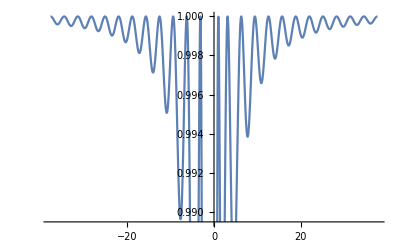

```mathematica
Plot[(x^2+Sin[x] Sinc[x])/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2))),{x,-37.69911184307752,37.69911184307752}]
```

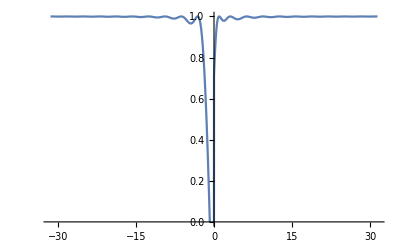

```mathematica
Plot[(x^2+Sin[x] Sinc[x])/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2))),{x,-10π,10π},PlotRange->{0,1}]
```

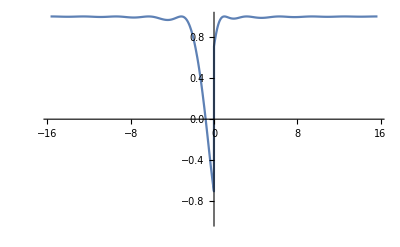

```mathematica
Plot[(x^2+Sin[x] Sinc[x])/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2))),{x,-5π,5π},PlotRange->{-1,1}]
```

```mathematica
(x^2+Sin[x] Sinc[x])/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2)))Sin[x]
```

(Sin[x] (x^2+Sin[x] Sinc[x]))/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2)))

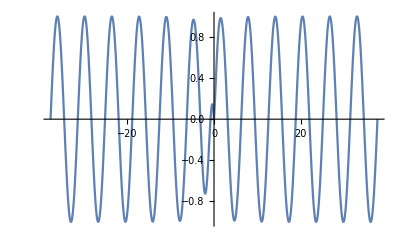

```mathematica
Plot[(Sin[x] (x^2+Sin[x] Sinc[x]))/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2))),{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
(1-a[x])p[x]+ a[x] q[x]
```

(1-a[x]) p[x]+a[x] q[x]

```mathematica
With[{a=Sin,p=Identity,q=Log},
(1-a[x])p[x]+ a[x] q[x]
]
```

x (1-Sin[x])+Log[x] Sin[x]

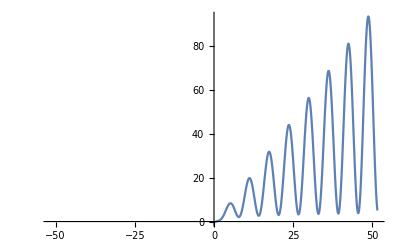

```mathematica
Plot[x (1-Sin[x])+Log[x] Sin[x],{x,-51.6238898038469,51.6238898038469}]
```

```mathematica
(1+Cos[π θ])/2
```

1/2 (1+Cos[π θ])

```mathematica
With[{a=Function[x,1/2 (1+Cos[π x])],p=Identity,q=Log},
(1-a[x])p[x]+ a[x] q[x]
]
```

x (1+1/2 (-1-Cos[π x]))+1/2 (1+Cos[π x]) Log[x]

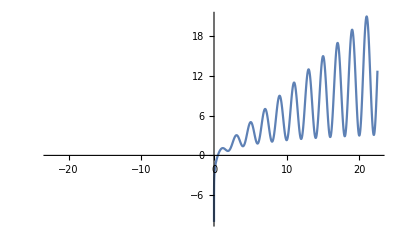

```mathematica
Plot[x (1+1/2 (-1-Cos[π x]))+1/2 (1+Cos[π x]) Log[x],{x,-22.5,22.5}]
```

```mathematica
With[{a=Function[x,1/2 (1+Cos[π x])],p=Identity,q=Function[x,x^3]},
(1-a[x])p[x]+ a[x] q[x]
]
```

x (1+1/2 (-1-Cos[π x]))+1/2 x^3 (1+Cos[π x])

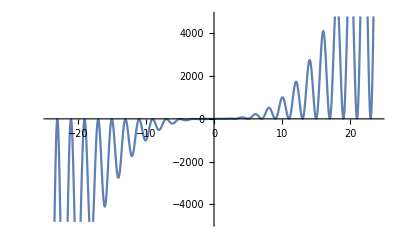

```mathematica
Plot[x (1+1/2 (-1-Cos[π x]))+1/2 x^3 (1+Cos[π x]),{x,-24.,24.}]
```

```mathematica
FullSimplify[
(1-a[x])p[x]+ a[x] q[x],
{x,a[x],p[x],q[x]}∈Reals∧0≤a[x]≤1]
```

p[x]-a[x] p[x]+a[x] q[x]

```mathematica
FullSimplify[
Normalize@{x,(1-a[x])p[x]+ a[x] q[x]}.
Normalize@{x,q[x]},
{x,a[x],p[x],q[x]}∈Reals∧0≤a[x]≤1]
```

(x^2+q[x] (p[x]-a[x] p[x]+a[x] q[x]))/(√((x^2+q[x]^2) (x^2+(p[x]-a[x] p[x]+a[x] q[x])^2)))

```mathematica
(x^2+Sin[x] Sinc[x])/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2)))Sinc[x]
```

(Sinc[x] (x^2+Sin[x] Sinc[x]))/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2)))

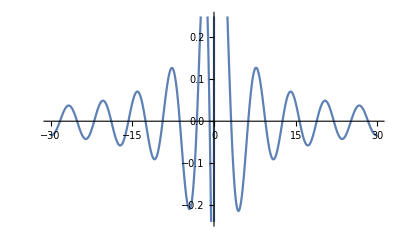

```mathematica
Plot[(Sinc[x] (x^2+Sin[x] Sinc[x]))/(√((x^2+Sin[x]^2) (x^2+Sinc[x]^2))),{x,-30,30}]
```

```mathematica
(x^2+q[x] (p[x]-a[x] p[x]+a[x] q[x]))/(√((x^2+q[x]^2) (x^2+(p[x]-a[x] p[x]+a[x] q[x])^2)))->a[x]
```

(x^2+q[x] (p[x]-a[x] p[x]+a[x] q[x]))/(√((x^2+q[x]^2) (x^2+(p[x]-a[x] p[x]+a[x] q[x])^2)))→a[x]

```mathematica
(x^2+q[x] g[x])/(√((x^2+q[x]^2) (x^2+g[x]^2)))
```

(x^2+g[x] q[x])/(√((x^2+g[x]^2) (x^2+q[x]^2)))

```mathematica
(x^2+q[x] (p[x]-a[x] p[x]+a[x] q[x]))/(√((x^2+q[x]^2) (x^2+(p[x]-a[x] p[x]+a[x] q[x])^2)))
```

(x^2+q[x] (p[x]-a[x] p[x]+a[x] q[x]))/(√((x^2+q[x]^2) (x^2+(p[x]-a[x] p[x]+a[x] q[x])^2)))